```mathematica
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

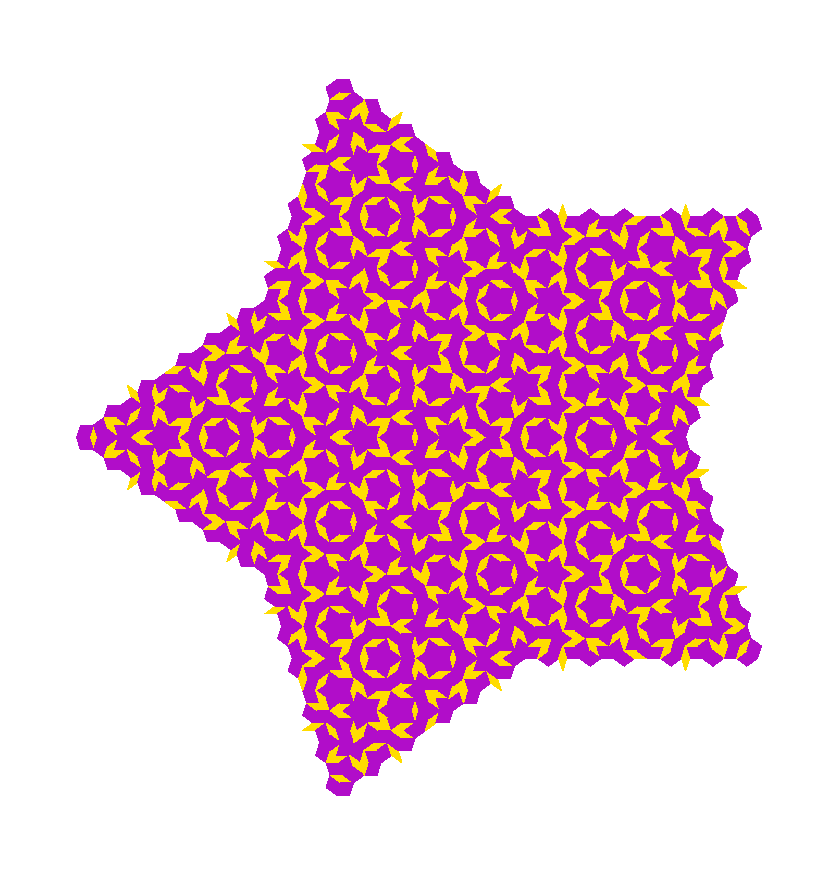

```mathematica
See@FullInflate[starseed,6]
```

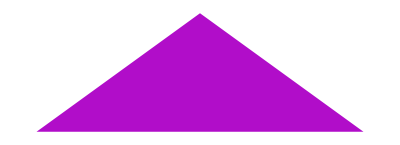

```mathematica
See@{unitfat}
```

```mathematica
Coor/@Δ/@{unitfat}
```

{{{-0.809017,0},{0.809017,0},{1.11022×10^-16,0.587785}}}

```mathematica
Graphics[Line[{{-0.8090169943749475,0},{0.8090169943749475,0}}]]
```

```mathematica
KitesEdges[{{A_,B_,C_},t_}]:=
If[t=="fat",Line[Coor[{A,B}]],Line[Coor[{B,C}]]]
```

```mathematica
{unitfat}
```

{{{-0.809017,0.809017,1.11022×10^-16+0.587785 ⅈ},fat}}

```mathematica
Coor[{-0.8090169943749475,0.8090169943749475}]
```

{{-0.809017,0},{0.809017,0}}

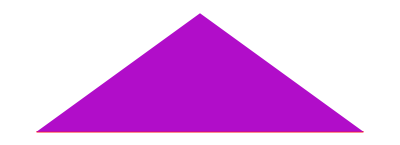

```mathematica
Show[Graphics[{Thick,Red,Kites[unitfat]}],See@{unitfat}]
```

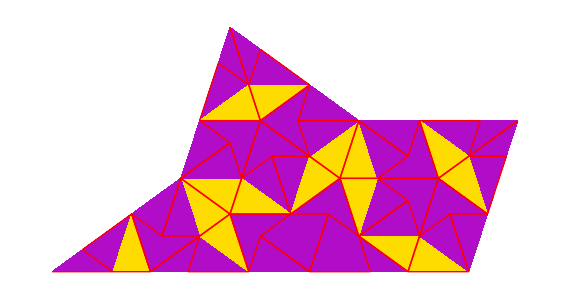

```mathematica
Show[See@Inflate[starseed,2],Graphics[{Red,Thick,KitesEdges/@Inflate[starseed,3]}]]
```

```mathematica
KiteBreak[{{A_,B_,C_},t_}]:=If[t=="fat",{{{A,C,A+(A-B)(1-ϕ)},"kite"},{{B,C,A+(A-B)(1-ϕ)},"dart"}},{{{A,B,C},"kite"}}]
KiteFill:=If[Last@#=="kite",{EdgeForm[NiceOrange],NiceOrange,Triangle@Coor@First@#},{EdgeForm[NiceBlue],NiceBlue,Triangle@Coor@First@#}]&
SeeKitesDatrts[list_]:= Graphics[Triangle/@Coor/@Flatten[KiteFill/@list,1]]
```

```mathematica
$MachinePrecision
```

10

```mathematica
$MinPrecision=300*$MachinePrecision
```

4786.38

```mathematica
$MinPrecision
```

47.8638

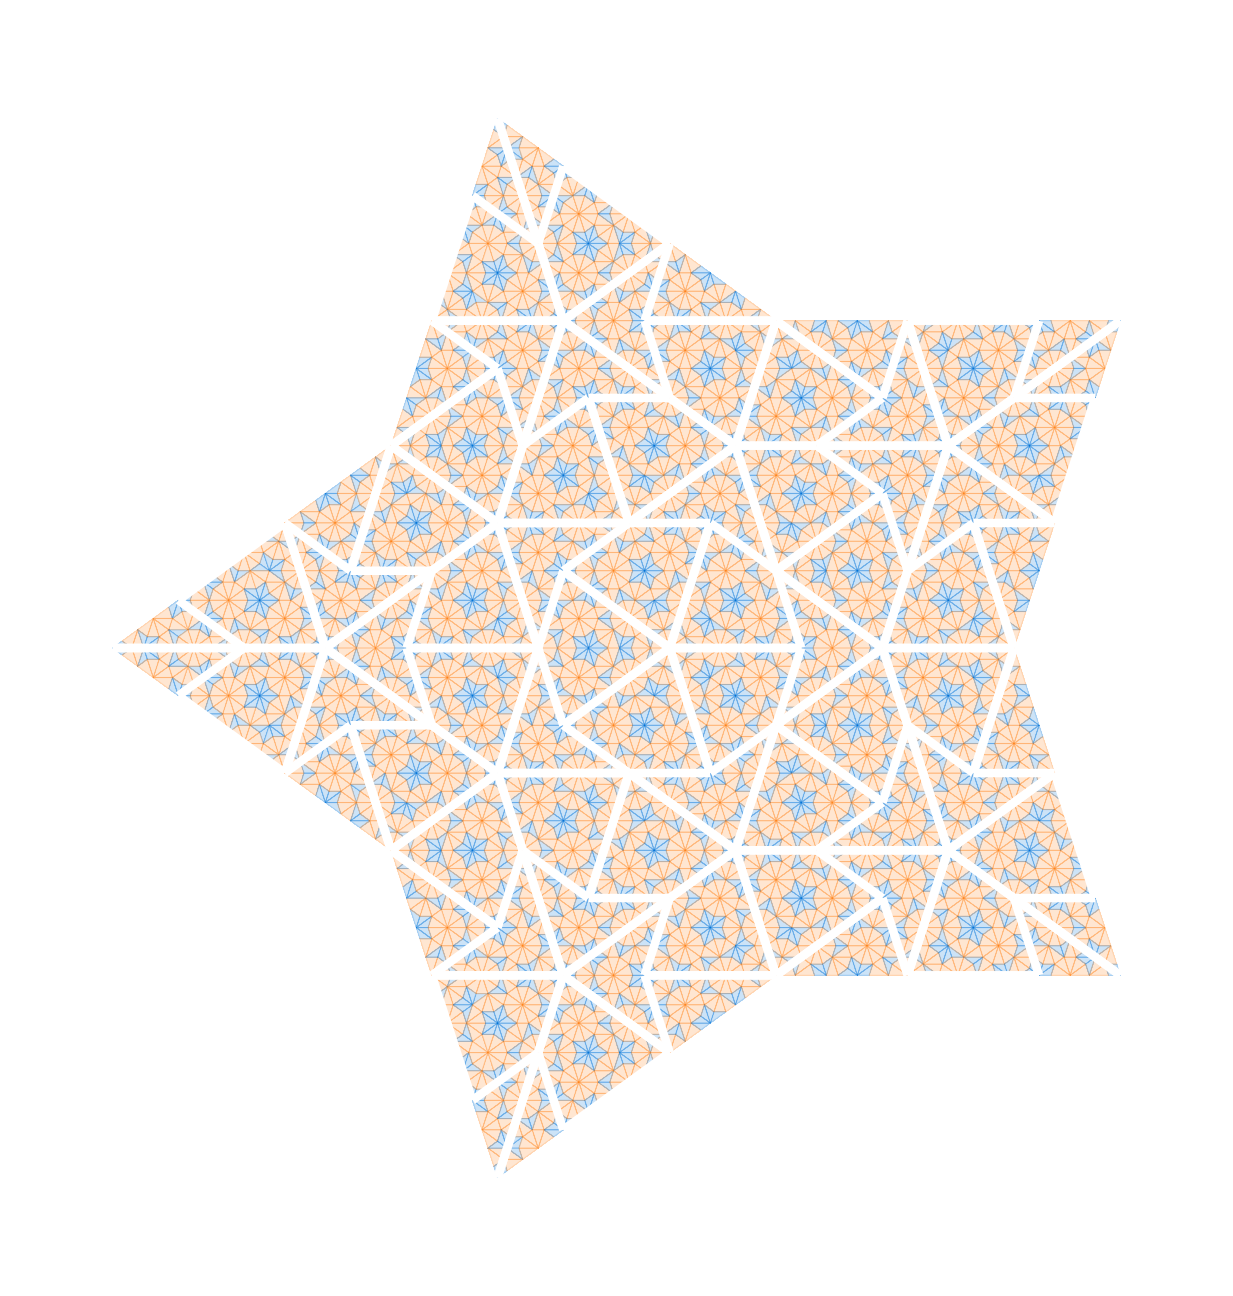

```mathematica
Show[Graphics[{Opacity[0.2],KiteFill/@AddConj@Flatten[KiteBreak/@Inflate[starseed,6],1]}],Graphics[{White,Thickness[0.005],KitesEdges/@AddConj@Inflate[starseed,3]}],PlotRange[]
```

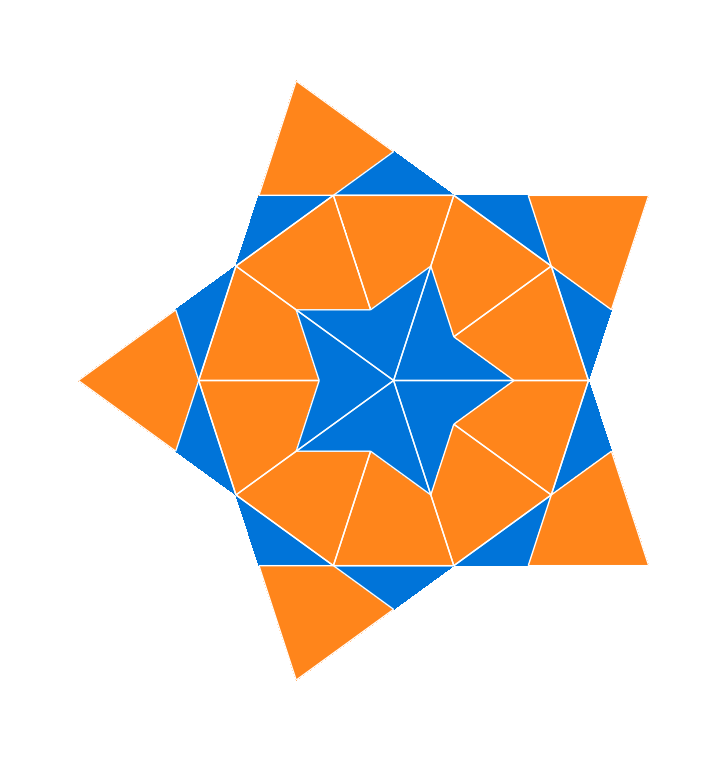

```mathematica
??FatInflate
```

Inflation Rules for fat triangles

FatInflate[{{a_,b_,c_},f_}]:=Block[{d=a+(c-a)/ϕ,e=a+(b-a)/ϕ},{Fat[{e,a,d}],Skinny[{d,c,e}],Fat[{b,c,e}]}]

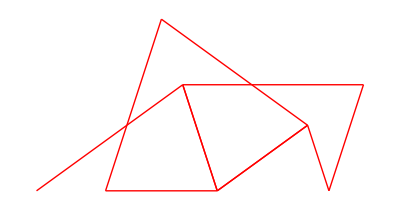

```mathematica
Graphics[{Red,Thick,Kites/@Inflate[starseed,1]}]
```

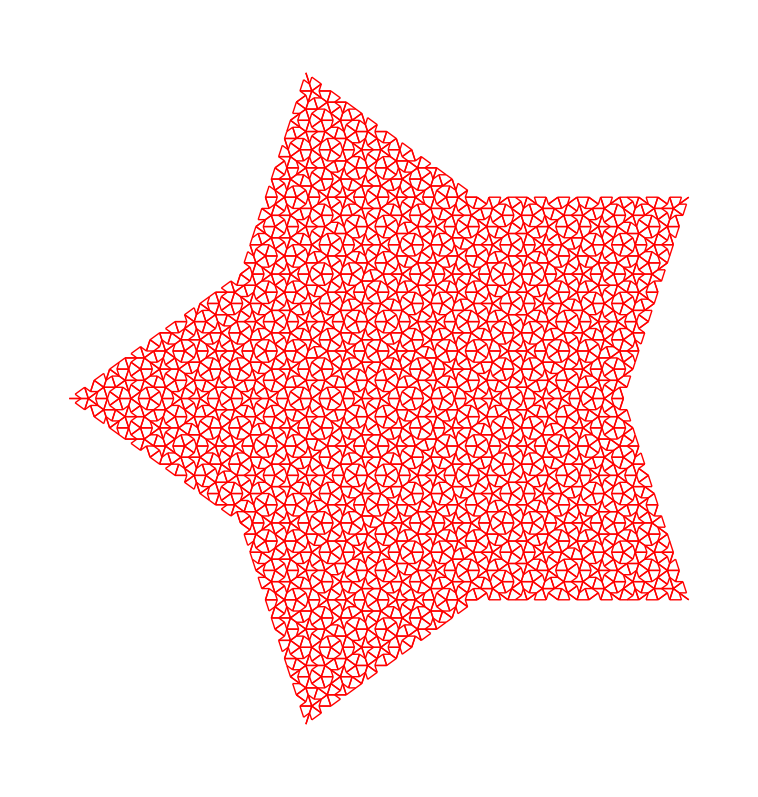

```mathematica
Graphics[{Red,Thick,Kites/@AddConj[Inflate[starseed,7]]}]
```

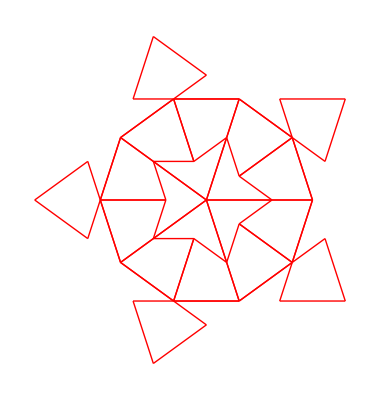
```mathematica
-Graphics-3
```

3 -Graphics-

```mathematica
??FullInflate
```

Inflates, Conjugates, Culls, and Converts to Rhombs

FullInflate[seed_,n_]:=Rhomb/@Cull[AddConj[Inflate[seed,n]]]